```mathematica
AppendTo[$Path, NotebookDirectory[]];
```

```mathematica
Get["CubeAcquire.wl"]
Get["CubeVisualize.wl"]
Get["CubeCore.wl"]
```

```mathematica
cubeString = sampleStrings["solved"]
```

WWWWWWWWWOOOGGGRRRBBBOOOGGGRRRBBBOOOGGGRRRBBBYYYYYYYYY

## 2D Cube

```mathematica
cube2D = Generate2DCube[cubeString];
```

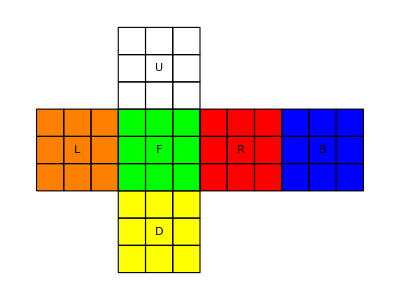

```mathematica
Visualize2DCube[cube2D];
```

## 3D Cube

```mathematica
cube3DPieces = GetPieces[cubeString];
```

```mathematica
cube3D = Dynamic[Generate3DCube[cube3DPieces]];
```

```mathematica
Visualize3DCube[cube3D];
```

-Graphics3D-

### Controlli

#### Generale

```mathematica
List[
Button["Load solved",cube3DPieces=GetPieces[sampleStrings["solved"]];],
Button["Load start",cube3DPieces=GetPieces[sampleStrings["start"]];]
]
```

{Load solved,Load start}

#### Mosse standard cubo

```mathematica
List[Button["L",cube3DPieces=RotateL[cube3DPieces];],Button["L'",cube3DPieces=RotateLi[cube3DPieces];],Button["R",cube3DPieces=RotateR[cube3DPieces];],Button["R'",cube3DPieces=RotateRi[cube3DPieces];],Button["U",cube3DPieces=RotateU[cube3DPieces];],Button["U'",cube3DPieces=RotateUi[cube3DPieces];],Button["D",cube3DPieces=RotateD[cube3DPieces];],Button["D'",cube3DPieces=RotateDi[cube3DPieces];],Button["F",cube3DPieces=RotateF[cube3DPieces];],Button["F'",cube3DPieces=RotateFi[cube3DPieces];],Button["B",cube3DPieces=RotateB[cube3DPieces];],Button["B'",cube3DPieces=RotateBi[cube3DPieces];]]
```

{L,L',R,R',U,U',D,D',F,F',B,B'}

#### Rotazione cubo

```mathematica
List[Button["X",cube3DPieces=RotateX[cube3DPieces];],Button["X'",cube3DPieces=RotateXi[cube3DPieces];],Button["Y",cube3DPieces=RotateY[cube3DPieces];],Button["Y'",cube3DPieces=RotateYi[cube3DPieces];],Button["Z",cube3DPieces=RotateZ[cube3DPieces];],Button["Z'",cube3DPieces=RotateZi[cube3DPieces];]]
```

{X,X',Y,Y',Z,Z'}